```mathematica
Total[Select[Range[2,9999],IsAmicable]]
```

40284

```mathematica
1==2
```

False

```mathematica
DivisorSigma[1,10]
```

18

```mathematica
DivisorSigma[1,DivisorSigma[1,220]]
```

1560

```mathematica
ProperDivisor=DivisorSigma[1,#]-#&
```

DivisorSigma[1,#1]-#1&

```mathematica
ProperDivisor[10]
```

8

```mathematica
ProperDivisor[220]
```

284

```mathematica
ProperDivisor[ProperDivisor[220]]
```

220

```mathematica
IsAmicable=And[ProperDivisor[ProperDivisor[#]]==#,#≠ProperDivisor[#]]&
```

ProperDivisor[ProperDivisor[#1]]==#1&&#1≠ProperDivisor[#1]&

```mathematica
IsAmicable[6]
```

False

```mathematica
IsAmicable[ProperDivisor[220]]
```

True

```mathematica
IsAmicable[1]
```

DivisorSigma[1,0]==1

```mathematica
DivisorSigma[2]
```

DivisorSigma::argr: DivisorSigma called with 1 argument; 2 arguments are expected.

DivisorSigma[2]

```mathematica
IsAmicable[2]
```

False

```mathematica
Total[Select[Range[2,9999],IsAmicable]]
```

31626

```mathematica
Select[Range[2,9999],IsAmicable]
```

{6,28,220,284,496,1184,1210,2620,2924,5020,5564,6232,6368,8128}

```mathematica
Length[{6,28,220,284,496,1184,1210,2620,2924,5020,5564,6232,6368,8128}]
```

14

```mathematica
IsAbundant=ProperDivisor[#]>#&
```

ProperDivisor[#1]>#1&

```mathematica
ProperDivisor[12]
```

16

```mathematica
IsAbundant[12]
```

True

```mathematica
AbundantList=Select[Range[1,28123],IsAbundant];
```

```mathematica
Tuples[{1,2},{3,4}]
```

{{{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,2}},{{1,1,1,1},{1,1,1,1},{1,1,2,1}},«4090»,{{2,2,2,2},{2,2,2,2},{2,2,1,2}},{{2,2,2,2},{2,2,2,2},{2,2,2,1}},{{2,2,2,2},{2,2,2,2},{2,2,2,2}}}

```mathematica
Tuples[{{1,2},{3,4}}]
```

{{1,3},{1,4},{2,3},{2,4}}

```mathematica
Map[Total,Tuples[{{1,2},{3,4}}]]
```

{4,5,5,6}

```mathematica
AbundantSums=DeleteDuplicates[Map[Total,Tuples[AbundantList,2]]];
```

```mathematica
1∈{1,2,3}
```

1∈{1,2,3}

```mathematica
Element[1,{1,2,3}]
```

1∈{1,2,3}

```mathematica
Select[Range[1,28123],Not[MemberQ[AbundantSums,#]]&]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,25,26,27,28,29,31,33,34,35,37,39,41,43,45,46,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255,257,259,261,263,265,267,269,271,273,275,277,279,281,283,285,287,289,291,293,295,297,299,301,303,305,307,309,311,313,315,317,319,321,323,325,327,329,331,333,335,337,339,341,343,345,347,349,351,353,355,357,359,361,363,365,367,369,371,373,375,377,379,381,383,385,387,389,391,393,395,397,399,401,403,405,407,409,411,413,415,417,419,421,423,425,427,429,431,433,435,437,439,441,443,445,447,449,451,453,455,457,459,461,463,465,467,469,471,473,475,477,479,481,483,485,487,489,491,493,495,497,499,501,503,505,507,509,511,513,515,517,519,521,523,525,527,529,531,533,535,537,539,541,543,545,547,549,551,553,555,557,559,561,563,565,567,569,571,573,575,577,579,581,583,585,587,589,591,593,595,597,599,601,603,605,607,609,611,613,615,617,619,621,623,625,627,629,631,633,635,637,639,641,643,645,647,649,651,653,655,657,659,661,663,665,667,669,671,673,675,677,679,681,683,685,687,689,691,693,695,697,699,701,703,705,707,709,711,713,715,717,719,721,723,725,727,729,731,733,735,737,739,741,743,745,747,749,751,753,755,757,759,761,763,765,767,769,771,773,775,777,779,781,783,785,787,789,791,793,795,797,799,801,803,805,807,809,811,813,815,817,819,821,823,825,827,829,831,833,835,837,839,841,843,845,847,849,851,853,855,857,859,861,863,865,867,869,871,873,875,877,879,881,883,885,887,889,891,893,895,897,899,901,903,905,907,909,911,913,915,917,919,921,923,925,927,929,931,933,935,937,939,941,943,945,947,949,951,953,955,959,961,967,971,973,977,979,983,989,991,995,997,1003,1007,1009,1013,1019,1021,1027,1031,1037,1039,1043,1051,1055,1061,1063,1067,1069,1073,1075,1079,1081,1087,1091,1093,1097,1099,1103,1109,1111,1115,1117,1123,1127,1129,1133,1135,1139,1147,1151,1157,1159,1163,1171,1175,1177,1181,1183,1187,1189,1193,1195,1199,1201,1207,1211,1213,1219,1223,1229,1231,1235,1237,1241,1243,1247,1255,1259,1261,1267,1271,1273,1277,1279,1283,1289,1291,1301,1303,1307,1315,1319,1321,1327,1331,1333,1339,1343,1349,1351,1355,1357,1363,1367,1369,1373,1375,1379,1381,1387,1391,1397,1399,1403,1411,1415,1417,1423,1427,1429,1433,1439,1441,1447,1451,1453,1457,1459,1463,1469,1471,1475,1481,1483,1487,1493,1499,1501,1507,1511,1513,1519,1523,1529,1531,1535,1537,1541,1543,1547,1549,1555,1559,1567,1571,1573,1577,1579,1583,1591,1597,1601,1603,1607,1609,1613,1619,1621,1627,1633,1637,1639,1643,1651,1657,1661,1667,1669,1691,1697,1699,1703,1709,1711,1717,1721,1723,1727,1733,1739,1741,1747,1753,1759,1763,1769,1787,1789,1793,1801,1807,1811,1817,1819,1823,1829,1831,1837,1843,1849,1853,1859,1861,1867,1871,1877,1889,1891,1901,1903,1907,1909,1919,1921,1931,1933,1949,1951,1957,1961,1963,1969,1973,1979,1987,1993,1997,1999,2003,2011,2017,2021,2027,2029,2041,2047,2053,2057,2059,2063,2069,2071,2077,2081,2083,2087,2099,2101,2111,2113,2117,2123,2131,2137,2141,2143,2153,2159,2167,2171,2173,2179,2189,2197,2201,2203,2207,2209,2213,2221,2227,2231,2237,2239,2243,2249,2251,2263,2267,2269,2273,2281,2287,2291,2299,2327,2329,2333,2339,2341,2347,2351,2357,2363,2369,2371,2377,2383,2389,2393,2399,2419,2423,2431,2437,2447,2453,2459,2461,2467,2473,2479,2483,2489,2491,2497,2501,2507,2519,2521,2531,2533,2537,2539,2549,2551,2561,2563,2579,2581,2587,2591,2593,2599,2603,2623,2627,2629,2633,2647,2651,2657,2659,2671,2677,2683,2687,2689,2693,2699,2701,2707,2711,2717,2729,2731,2741,2743,2747,2753,2761,2767,2771,2773,2783,2789,2797,2803,2809,2819,2827,2831,2837,2839,2843,2851,2857,2861,2867,2869,2873,2879,2893,2899,2903,2911,2917,2957,2959,2963,2971,2977,2981,2987,2993,2999,3001,3007,3013,3019,3023,3029,3049,3053,3061,3067,3077,3083,3089,3091,3097,3103,3109,3113,3119,3127,3131,3137,3149,3151,3161,3163,3167,3169,3179,3181,3191,3193,3209,3211,3217,3221,3223,3229,3253,3257,3259,3263,3277,3281,3287,3289,3301,3307,3317,3319,3323,3329,3331,3341,3347,3359,3361,3371,3373,3383,3391,3397,3401,3403,3413,3419,3427,3433,3439,3449,3457,3461,3467,3469,3473,3481,3487,3491,3499,3503,3509,3523,3533,3541,3547,3587,3589,3593,3601,3607,3611,3617,3623,3629,3631,3637,3643,3653,3659,3679,3683,3691,3707,3713,3719,3721,3727,3733,3739,3743,3749,3757,3767,3779,3781,3791,3793,3797,3799,3809,3811,3821,3823,3839,3841,3847,3851,3853,3859,3883,3887,3893,3907,3911,3917,3919,3931,3947,3949,3959,3971,3977,3989,3991,4001,4003,4013,4021,4027,4031,4033,4043,4049,4057,4063,4069,4079,4087,4091,4097,4099,4103,4111,4117,4121,4129,4133,4139,4153,4163,4171,4177,4217,4219,4223,4231,4237,4241,4247,4253,4259,4261,4267,4283,4309,4313,4321,4343,4349,4351,4357,4363,4369,4373,4379,4387,4397,4409,4411,4421,4423,4427,4429,4439,4451,4453,4469,4471,4477,4483,4489,4513,4517,4523,4537,4541,4547,4549,4561,4577,4579,4589,4601,4607,4619,4621,4631,4633,4643,4651,4661,4663,4673,4679,4687,4693,4699,4709,4717,4727,4733,4741,4747,4751,4759,4763,4769,4783,4801,4807,4847,4853,4861,4867,4871,4877,4883,4891,4939,4943,4951,4973,4979,4981,4987,4999,5003,5009,5017,5027,5039,5041,5051,5053,5057,5059,5069,5083,5099,5101,5107,5113,5119,5143,5147,5153,5167,5171,5177,5179,5191,5207,5219,5231,5237,5249,5251,5261,5263,5273,5281,5291,5293,5303,5309,5317,5323,5329,5339,5347,5357,5363,5371,5377,5381,5389,5393,5399,5413,5431,5437,5477,5483,5491,5497,5501,5507,5513,5573,5581,5603,5611,5629,5633,5639,5647,5669,5671,5683,5687,5689,5699,5713,5731,5737,5743,5749,5773,5777,5783,5797,5801,5807,5821,5837,5849,5861,5867,5881,5891,5893,5903,5911,5921,5923,5933,5939,5947,5953,5959,5969,5987,5993,6007,6011,6019,6023,6029,6043,6061,6067,6107,6121,6131,6203,6211,6233,6241,6259,6263,6269,6277,6299,6301,6317,6329,6343,6361,6367,6373,6379,6403,6407,6413,6427,6431,6437,6451,6467,6497,6509,6533,6541,6551,6553,6563,6583,6589,6599,6617,6623,6637,6653,6673,6691,6697,6737,6751,6757,6761,6773,6871,6889,6893,6907,6931,6947,6949,6973,6997,7003,7009,7037,7057,7061,7067,7109,7121,7141,7181,7213,7229,7253,7283,7321,7327,7367,7381,7391,7493,7501,7519,7577,7589,7603,7627,7673,7687,7691,7739,7757,7769,7771,7801,7813,7849,7859,7877,7883,7933,8011,8021,8123,8149,8159,8191,8219,8251,8269,8303,8317,8401,8431,8441,8443,8473,8581,8587,8627,8651,8663,8837,8839,8887,8923,8933,8951,8957,9017,9061,9071,9073,9109,9137,9211,9391,9419,9467,9517,9587,9617,9701,9733,10331,10363,10471,10541,10679,10951,10993,11591,11801,12013,12361,12407,12569,12619,12731,12851,13037,13297,13309,13621,13829,13879,14143,14251,14297,15371,15557,16187,17261,17891,18437,19067,20161}

```mathematica
AbundantSums
```

{24,30,32,36,42,48,52,54,60,66,68,72,78,82,84,90,92,96,100,102,108,112,114,116,120,124,«53819»,56194,56196,56200,56202,56204,56206,56198,56208,56212,56214,56210,56218,56220,56216,56222,56224,56226,56230,56232,56228,56234,56236,56238,56240,56242,56244}

```mathematica
MemberQ[AbundantSums,2]
```

False

```mathematica
Not[MemberQ[AbundantSums,2]]
```

True

```mathematica
Select[{1,2},MemberQ]
```

MemberQ::argtu: MemberQ called with 1 argument; 2 or 3 arguments are expected.

{}

```mathematica
Total[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,25,26,27,28,29,31,33,34,35,37,39,41,43,45,46,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,105,107,109,111,113,115,117,119,121,123,125,127,129,131,133,135,137,139,141,143,145,147,149,151,153,155,157,159,161,163,165,167,169,171,173,175,177,179,181,183,185,187,189,191,193,195,197,199,201,203,205,207,209,211,213,215,217,219,221,223,225,227,229,231,233,235,237,239,241,243,245,247,249,251,253,255,257,259,261,263,265,267,269,271,273,275,277,279,281,283,285,287,289,291,293,295,297,299,301,303,305,307,309,311,313,315,317,319,321,323,325,327,329,331,333,335,337,339,341,343,345,347,349,351,353,355,357,359,361,363,365,367,369,371,373,375,377,379,381,383,385,387,389,391,393,395,397,399,401,403,405,407,409,411,413,415,417,419,421,423,425,427,429,431,433,435,437,439,441,443,445,447,449,451,453,455,457,459,461,463,465,467,469,471,473,475,477,479,481,483,485,487,489,491,493,495,497,499,501,503,505,507,509,511,513,515,517,519,521,523,525,527,529,531,533,535,537,539,541,543,545,547,549,551,553,555,557,559,561,563,565,567,569,571,573,575,577,579,581,583,585,587,589,591,593,595,597,599,601,603,605,607,609,611,613,615,617,619,621,623,625,627,629,631,633,635,637,639,641,643,645,647,649,651,653,655,657,659,661,663,665,667,669,671,673,675,677,679,681,683,685,687,689,691,693,695,697,699,701,703,705,707,709,711,713,715,717,719,721,723,725,727,729,731,733,735,737,739,741,743,745,747,749,751,753,755,757,759,761,763,765,767,769,771,773,775,777,779,781,783,785,787,789,791,793,795,797,799,801,803,805,807,809,811,813,815,817,819,821,823,825,827,829,831,833,835,837,839,841,843,845,847,849,851,853,855,857,859,861,863,865,867,869,871,873,875,877,879,881,883,885,887,889,891,893,895,897,899,901,903,905,907,909,911,913,915,917,919,921,923,925,927,929,931,933,935,937,939,941,943,945,947,949,951,953,955,959,961,967,971,973,977,979,983,989,991,995,997,1003,1007,1009,1013,1019,1021,1027,1031,1037,1039,1043,1051,1055,1061,1063,1067,1069,1073,1075,1079,1081,1087,1091,1093,1097,1099,1103,1109,1111,1115,1117,1123,1127,1129,1133,1135,1139,1147,1151,1157,1159,1163,1171,1175,1177,1181,1183,1187,1189,1193,1195,1199,1201,1207,1211,1213,1219,1223,1229,1231,1235,1237,1241,1243,1247,1255,1259,1261,1267,1271,1273,1277,1279,1283,1289,1291,1301,1303,1307,1315,1319,1321,1327,1331,1333,1339,1343,1349,1351,1355,1357,1363,1367,1369,1373,1375,1379,1381,1387,1391,1397,1399,1403,1411,1415,1417,1423,1427,1429,1433,1439,1441,1447,1451,1453,1457,1459,1463,1469,1471,1475,1481,1483,1487,1493,1499,1501,1507,1511,1513,1519,1523,1529,1531,1535,1537,1541,1543,1547,1549,1555,1559,1567,1571,1573,1577,1579,1583,1591,1597,1601,1603,1607,1609,1613,1619,1621,1627,1633,1637,1639,1643,1651,1657,1661,1667,1669,1691,1697,1699,1703,1709,1711,1717,1721,1723,1727,1733,1739,1741,1747,1753,1759,1763,1769,1787,1789,1793,1801,1807,1811,1817,1819,1823,1829,1831,1837,1843,1849,1853,1859,1861,1867,1871,1877,1889,1891,1901,1903,1907,1909,1919,1921,1931,1933,1949,1951,1957,1961,1963,1969,1973,1979,1987,1993,1997,1999,2003,2011,2017,2021,2027,2029,2041,2047,2053,2057,2059,2063,2069,2071,2077,2081,2083,2087,2099,2101,2111,2113,2117,2123,2131,2137,2141,2143,2153,2159,2167,2171,2173,2179,2189,2197,2201,2203,2207,2209,2213,2221,2227,2231,2237,2239,2243,2249,2251,2263,2267,2269,2273,2281,2287,2291,2299,2327,2329,2333,2339,2341,2347,2351,2357,2363,2369,2371,2377,2383,2389,2393,2399,2419,2423,2431,2437,2447,2453,2459,2461,2467,2473,2479,2483,2489,2491,2497,2501,2507,2519,2521,2531,2533,2537,2539,2549,2551,2561,2563,2579,2581,2587,2591,2593,2599,2603,2623,2627,2629,2633,2647,2651,2657,2659,2671,2677,2683,2687,2689,2693,2699,2701,2707,2711,2717,2729,2731,2741,2743,2747,2753,2761,2767,2771,2773,2783,2789,2797,2803,2809,2819,2827,2831,2837,2839,2843,2851,2857,2861,2867,2869,2873,2879,2893,2899,2903,2911,2917,2957,2959,2963,2971,2977,2981,2987,2993,2999,3001,3007,3013,3019,3023,3029,3049,3053,3061,3067,3077,3083,3089,3091,3097,3103,3109,3113,3119,3127,3131,3137,3149,3151,3161,3163,3167,3169,3179,3181,3191,3193,3209,3211,3217,3221,3223,3229,3253,3257,3259,3263,3277,3281,3287,3289,3301,3307,3317,3319,3323,3329,3331,3341,3347,3359,3361,3371,3373,3383,3391,3397,3401,3403,3413,3419,3427,3433,3439,3449,3457,3461,3467,3469,3473,3481,3487,3491,3499,3503,3509,3523,3533,3541,3547,3587,3589,3593,3601,3607,3611,3617,3623,3629,3631,3637,3643,3653,3659,3679,3683,3691,3707,3713,3719,3721,3727,3733,3739,3743,3749,3757,3767,3779,3781,3791,3793,3797,3799,3809,3811,3821,3823,3839,3841,3847,3851,3853,3859,3883,3887,3893,3907,3911,3917,3919,3931,3947,3949,3959,3971,3977,3989,3991,4001,4003,4013,4021,4027,4031,4033,4043,4049,4057,4063,4069,4079,4087,4091,4097,4099,4103,4111,4117,4121,4129,4133,4139,4153,4163,4171,4177,4217,4219,4223,4231,4237,4241,4247,4253,4259,4261,4267,4283,4309,4313,4321,4343,4349,4351,4357,4363,4369,4373,4379,4387,4397,4409,4411,4421,4423,4427,4429,4439,4451,4453,4469,4471,4477,4483,4489,4513,4517,4523,4537,4541,4547,4549,4561,4577,4579,4589,4601,4607,4619,4621,4631,4633,4643,4651,4661,4663,4673,4679,4687,4693,4699,4709,4717,4727,4733,4741,4747,4751,4759,4763,4769,4783,4801,4807,4847,4853,4861,4867,4871,4877,4883,4891,4939,4943,4951,4973,4979,4981,4987,4999,5003,5009,5017,5027,5039,5041,5051,5053,5057,5059,5069,5083,5099,5101,5107,5113,5119,5143,5147,5153,5167,5171,5177,5179,5191,5207,5219,5231,5237,5249,5251,5261,5263,5273,5281,5291,5293,5303,5309,5317,5323,5329,5339,5347,5357,5363,5371,5377,5381,5389,5393,5399,5413,5431,5437,5477,5483,5491,5497,5501,5507,5513,5573,5581,5603,5611,5629,5633,5639,5647,5669,5671,5683,5687,5689,5699,5713,5731,5737,5743,5749,5773,5777,5783,5797,5801,5807,5821,5837,5849,5861,5867,5881,5891,5893,5903,5911,5921,5923,5933,5939,5947,5953,5959,5969,5987,5993,6007,6011,6019,6023,6029,6043,6061,6067,6107,6121,6131,6203,6211,6233,6241,6259,6263,6269,6277,6299,6301,6317,6329,6343,6361,6367,6373,6379,6403,6407,6413,6427,6431,6437,6451,6467,6497,6509,6533,6541,6551,6553,6563,6583,6589,6599,6617,6623,6637,6653,6673,6691,6697,6737,6751,6757,6761,6773,6871,6889,6893,6907,6931,6947,6949,6973,6997,7003,7009,7037,7057,7061,7067,7109,7121,7141,7181,7213,7229,7253,7283,7321,7327,7367,7381,7391,7493,7501,7519,7577,7589,7603,7627,7673,7687,7691,7739,7757,7769,7771,7801,7813,7849,7859,7877,7883,7933,8011,8021,8123,8149,8159,8191,8219,8251,8269,8303,8317,8401,8431,8441,8443,8473,8581,8587,8627,8651,8663,8837,8839,8887,8923,8933,8951,8957,9017,9061,9071,9073,9109,9137,9211,9391,9419,9467,9517,9587,9617,9701,9733,10331,10363,10471,10541,10679,10951,10993,11591,11801,12013,12361,12407,12569,12619,12731,12851,13037,13297,13309,13621,13829,13879,14143,14251,14297,15371,15557,16187,17261,17891,18437,19067,20161}]
```

4179871

```mathematica
1000000/9!
```

3125/1134

```mathematica
IntegerPart[3125/1134]
```

2

```mathematica
1000000-2*9!
```

274240

```mathematica
IntegerPart[3125/1134]
```

```mathematica
274240/8!
```

857/126

```mathematica
N[857/126]
```

6.80159

```mathematica
IntegerPart[857/126]
```

6

```mathematica
274240-6*8!
```

32320

```mathematica
274240-7*8!
```

-8000

```mathematica
32320/7!
```

404/63

```mathematica
IntegerPart[404/63]
```

6

```mathematica
32320/7!
```

404/63

```mathematica
N[404/9]
```

44.8889

```mathematica
32320-6*7!
```

2080

```mathematica
2080/6!
```

26/9

```mathematica
IntegerPart[26/9]
```

2

```mathematica
2080-2*6!
```

640

```mathematica
640/5!
```

16/3

```mathematica
IntegerPart[16/3]
```

5

```mathematica
640-5*5!
```

40

```mathematica
40/4!
```

5/3

```mathematica
IntegerPart[5/3]
```

1

```mathematica
274240/8!
```

857/126

```mathematica
IntegerPart[857/126]
```

6

```mathematica
274240-6*8!
```

32320

```mathematica
32320/7!
```

404/63

```mathematica
IntegerPart[404/63]
```

6

```mathematica
32320-6*7!
```

2080

```mathematica
IntegerPart[2080/6!]
```

2

```mathematica
2080-2*6!
```

640

```mathematica
640/5!
```

16/3

```mathematica
IntegerPart[16/3]
```

5

```mathematica
640-5*5!
```

40

```mathematica
IntegerPart[40/4!]
```

1

```mathematica
4!
```

24

```mathematica
IntegerPart[16/3!]
```

2

```mathematica
Hold[1+2]
```

Hold[1+2]

```mathematica
ReleaseHold[Hold[1+2]]
```

3

```mathematica
IntegerDigits[3]
```

{3}

```mathematica
Length[IntegerDigits[3]]
```

1

```mathematica
Fibonacci[1]
```

1

```mathematica
Fibonacci[2.5]
```

1.48931

```mathematica
Fibonacci[5,x]
```

1+3 x^2+x^4

```mathematica
Fibonacci[n]
```

Fibonacci[n]

```mathematica
Log[10,FunctionExpand[Fibonacci[x]]]
```

Log[((1/2 (1+√5))^x-(2/(1+√5))^x Cos[π x])/(√5)]/Log[10]

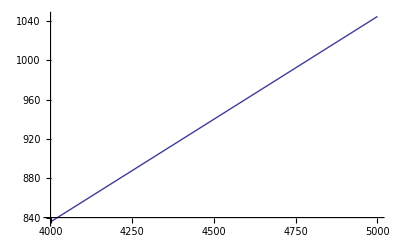

```mathematica
Plot[Log[((1/2 (1+√5))^x-(2/(1+√5))^x Cos[π x])/(√5)]/Log[10],{x,4000,5000}]
```

```mathematica
NSolve[Log[((1/2 (1+√5))^x-(2/(1+√5))^x Cos[π x])/(√5)]/Log[10]==1000,x,Reals]
```

$Aborted

```mathematica
Plot[Log[((1/2 (1+√5))^x-(2/(1+√5))^x Cos[π x])/(√5)]/Log[10],{x,4780,4790}]
```

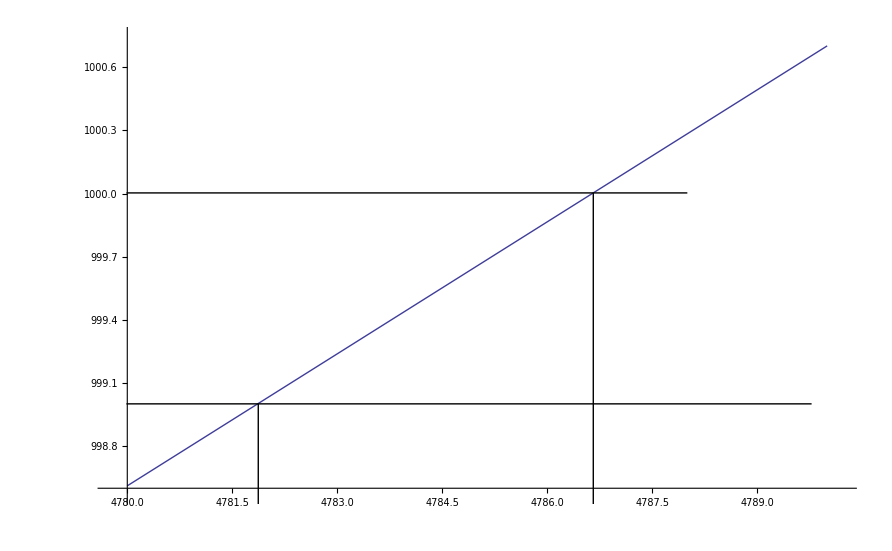

```mathematica
Length[IntegerDigits[Fibonacci[4785]]]
```

1000

```mathematica
Length[IntegerDigits[Fibonacci[4782]]]
```

1000

```mathematica
Fibonacci[4782]
```

1070066266382758936764980584457396885083683896632151665013235203375314520604694040621889147582489792657804694888177591957484336466672569959512996030461262748092482186144069433051234774442750273781753087579391666192149259186759553966422837148943113074699503439547001985432609723067290192870526447243726117715821825548491120525013201478612965931381792235559657452039506137551467837543229119602129934048260706175397706847068202895486902666185435124521900369480641357447470911707619766945691070098024393439617474103736912503231365532164773697023167755051595173518460579954919410967778373229665796581646513903488154256310184224190259846088000110186255550245493937113651657039447629584714548523425950428582425306083544435428212611008992863795048006894330309773217834864543113205765659868456288616808718693835297350643986297640660000723562917905207051164077614812491885830945940566688339109350944456576357666151619317753792891661581327159616877487983821820492520348473874384736771934512787029218636250627816

```mathematica
TextRecognize[-Graphics-]
```

50245

```mathematica
1/15
```

1/15

```mathematica
N[1/15]
```

0.0666667

```mathematica
1/27
```

1/27

```mathematica
N[1/21]
```

0.047619

```mathematica
N[1/21,20]
```

0.047619047619047619048

```mathematica
MultiplicativeOrder[10,21]
```

6

```mathematica
N[1/150,20]
```

0.0066666666666666666667

```mathematica
N[1/150,24]
```

0.00666666666666666666666667

```mathematica
Range[2,999];
```

```mathematica
relativeprimeto10=Select[Range[2,999],GCD[#,10]==1&]
```

{3,7,9,11,13,17,19,21,23,27,29,31,33,37,39,41,43,47,49,51,53,57,59,61,63,67,69,71,73,77,79,81,83,87,89,91,93,97,99,101,103,107,109,111,113,117,119,121,123,127,129,131,133,137,139,141,143,147,149,151,153,157,159,161,163,167,169,171,173,177,179,181,183,187,189,191,193,197,199,201,203,207,209,211,213,217,219,221,223,227,229,231,233,237,239,241,243,247,249,251,253,257,259,261,263,267,269,271,273,277,279,281,283,287,289,291,293,297,299,301,303,307,309,311,313,317,319,321,323,327,329,331,333,337,339,341,343,347,349,351,353,357,359,361,363,367,369,371,373,377,379,381,383,387,389,391,393,397,399,401,403,407,409,411,413,417,419,421,423,427,429,431,433,437,439,441,443,447,449,451,453,457,459,461,463,467,469,471,473,477,479,481,483,487,489,491,493,497,499,501,503,507,509,511,513,517,519,521,523,527,529,531,533,537,539,541,543,547,549,551,553,557,559,561,563,567,569,571,573,577,579,581,583,587,589,591,593,597,599,601,603,607,609,611,613,617,619,621,623,627,629,631,633,637,639,641,643,647,649,651,653,657,659,661,663,667,669,671,673,677,679,681,683,687,689,691,693,697,699,701,703,707,709,711,713,717,719,721,723,727,729,731,733,737,739,741,743,747,749,751,753,757,759,761,763,767,769,771,773,777,779,781,783,787,789,791,793,797,799,801,803,807,809,811,813,817,819,821,823,827,829,831,833,837,839,841,843,847,849,851,853,857,859,861,863,867,869,871,873,877,879,881,883,887,889,891,893,897,899,901,903,907,909,911,913,917,919,921,923,927,929,931,933,937,939,941,943,947,949,951,953,957,959,961,963,967,969,971,973,977,979,981,983,987,989,991,993,997,999}

```mathematica
Last[SortBy[MapIndexed[{Select[Range[2,999],GCD[#,10]==1&][[First[#2]]],MultiplicativeOrder[10,#1]}&,Select[Range[2,999],GCD[#,10]==1&]],Last]]
```

{983,982}

```mathematica
f[i_]:=List[Length[RealDigits[1/i][[1,-1]]],i];
Last[Last[Sort[Array[f,999]]]]
```

983

```mathematica
f[12]
```

{1,12}

```mathematica
f[1/3]
```

{0,1/3}

```mathematica
RealDigits[1/6]
```

{{1,{6}},0}

```mathematica
RealDigits[19/7]
```

{{2,{7,1,4,2,8,5}},1}

```mathematica
N[19/7,20]
```

2.7142857142857142857

```mathematica
N[1/6,20]
```

0.16666666666666666667

```mathematica
RealDigits[13/6]
```

{{2,1,{6}},1}

```mathematica
FromDigits[{{2,1,{6}},1}]
```

13/6

```mathematica
Last[First[{{1,1,{6}},1}]]
```

{6}

```mathematica
Reduce[10^n≤n*9^5,n,Integers]
```

n==1||n==2||n==3||n==4||n==5

```mathematica
Range[10,999999]
```

{10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,«999922»,999966,999967,999968,999969,999970,999971,999972,999973,999974,999975,999976,999977,999978,999979,999980,999981,999982,999983,999984,999985,999986,999987,999988,999989,999990,999991,999992,999993,999994,999995,999996,999997,999998,999999}

```mathematica
Range[10,999999]
```

{10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,«999922»,999966,999967,999968,999969,999970,999971,999972,999973,999974,999975,999976,999977,999978,999979,999980,999981,999982,999983,999984,999985,999986,999987,999988,999989,999990,999991,999992,999993,999994,999995,999996,999997,999998,999999}

```mathematica
5*9^5
```

295245

```mathematica
Reduce[10^n≤(n+1)*9^5,n,Integers]
```

n==0||n==1||n==2||n==3||n==4||n==5

```mathematica
9^5*6
```

354294

```mathematica
5*9^5+2^5
```

295277

```mathematica
Range[2,295277];
```

```mathematica
Range[2,295277];
```

```mathematica
Map[IntegerDigits,{1,2,30}]
```

{{1},{2},{3,0}}

```mathematica
Tuples[{Range[0,9]}]
```

{{0},{1},{2},{3},{4},{5},{6},{7},{8},{9}}

```mathematica
Tuples[{Range[0,9], Range[1,9]}]
```

{{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{5,7},{5,8},{5,9},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{6,7},{6,8},{6,9},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{7,7},{7,8},{7,9},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{8,7},{8,8},{8,9},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{9,7},{9,8},{9,9}}

```mathematica
DeleteDuplicates[Mod[Map[Apply[(#1^2+#2^2)&,#]&,Tuples[{Range[0,9], Range[1,9]}]],10]]
```

{1,4,9,6,5,2,0,7,8,3}

```mathematica
Sort[{1,4,9,6,5,2,0,7,8,3}]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
Mod[{4,1},2]
```

{0,1}

```mathematica
3^5
```

243

```mathematica
2^5
```

32

```mathematica
Reduce[x≤5,x,x∈{1,2,3}]
```

Reduce::bdomv: Warning: x ∈ {1, 2, 3} is not a valid domain specification. Mathematica is assuming it is a variable to eliminate.

x≤5

```mathematica
4^5
```

1024

```mathematica
5^5
```

3125

```mathematica
4^5+4^5
```

2048

```mathematica
3^5+3^5+3^5
```

729

```mathematica
9^5
```

59049

```mathematica
7^5
```

16807

```mathematica
4^5
```

1024

```mathematica
6^5
```

7776

```mathematica
7^5
```

16807

```mathematica
4^5
```

1024

```mathematica
9999-6^5
```

2223

```mathematica
6^5+5^5
```

10901

```mathematica
6^5+4^5+4^5+2^5
```

9888

```mathematica
9^5+8^5+6^5+3^5+2^5
```

99868

```mathematica
6*9^5
```

354294

```mathematica
Union[{1,2},{2,3}]
```

{1,2,3}

```mathematica
AbsoluteTiming[Total[Select[Union[Range[10,22],
			Range[100,333],
			Range[1000,6442], 
			Range[10000,98632],
			Range[100000,295277]],
	SumFive@@IntegerDigits[#]==#&]]]
```

{4.37467,443839}

```mathematica
Total[{4150,4151,54748,92727,93084,194979}]
```

443839

```mathematica
Max[{4150,4151,54748,92727,93084,194979}]
```

194979

```mathematica
4^5+1^5+5^5
```

4150

```mathematica
SumFive@@IntegerDigits[123]
```

276

```mathematica
SumFive=Total[Map[#^5&,List[##]]]&
```

Total[(#1^5&)/@{##1}]&

```mathematica
SumFive[1,2,3]
```

276

```mathematica
Map[#^5&,{1,2,3}]
```

{1,32,243}

```mathematica
Total[{1,32,243}]
```

276

```mathematica
List[Sequence[1,2,3]]
```

{1,2,3}

```mathematica
Sequence[1,2,3]
```

Sequence[1,2,3]

```mathematica
AbsoluteTiming[isSum[n_,k_]:=n==Total[IntegerDigits[n]^k];
Total[Select[Table[i,{i,10^6}],isSum[#,5]&]]-1]
```

{5.55361,443839}

```mathematica
Clear[f];
```

```mathematica
sol=Reduce[200==200a+100b+50c+20d+10e+5f+2g+1h&&a≥0&&b≥0&&c≥0&&d≥0&&e≥0&&f≥0&&g≥0,{a,b,c,d,e,f,g},Integers]
```

(C[1]|C[2]|C[3]|C[4]|C[5]|C[6]|C[7])∈Integers&&C[1]≥0&&C[2]≥0&&C[3]≥0&&C[4]≥0&&C[5]≥0&&C[6]≥0&&C[7]≥0&&h==200-200 C[1]-100 C[2]-50 C[3]-20 C[4]-10 C[5]-5 C[6]-2 C[7]&&a==C[1]&&b==C[2]&&c==C[3]&&d==C[4]&&e==C[5]&&f==C[6]&&g==C[7]

```mathematica
{a,b,c,d,e,f,g}/.First[sol]/.Table[{C[1]->i},{i,10}]//Simplify
```

```mathematica
Table[{i},{i,10}]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}

```mathematica
Tuples[{
```

```mathematica
200^8
```

2560000000000000000

```mathematica
Tuples[Map[Range[1,200/#]&,{200,100,50,20,10,5,2,1}]]
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

SystemException[MemoryAllocationFailure,{Tuples[{{1},{1,2},{1,2,3,4},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}}]}]

```mathematica
Total@{1,2,3}
```

6

```mathematica
Map[Range[1,200/#]&,{200,100,50,20,10,5,2,1}]
```

{{1},{1,2},{1,2,3,4},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}}

```mathematica
Map[Length,%]
```

{1,2,4,10,20,40,100,200}

```mathematica
Total[{1,2,4,10,20,40,100,200}]
```

377

```mathematica
Product[%]
```

Product::argmu: Product called with 1 argument; 2 or more arguments are expected.

Product[%]

```mathematica
Fold[Times,1,{1,2,4,10,20,40,100,200}]
```

1280000000

```mathematica
Select[Tuples[Map[Range[1,200/#]&,{200,100,50,20,10,5,2,1}]],#1*200+#2*100+#3*50+#4*20+#5*10+#6*5+#7*2+#8*1==200&];
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

SystemException[MemoryAllocationFailure,{Select[Tuples[(Range[1,200/#1]&)/@{200,100,50,20,10,5,2,1}],#1 200+#2 100+#3 50+#4 20+#5 10+#6 5+#7 2+#8 1==200&];,Select[Tuples[(Range[1,200/#1]&)/@{200,100,50,20,10,5,2,1}],#1 200+#2 100+#3 50+#4 20+#5 10+#6 5+#7 2+#8 1==200&],Tuples[{{1},{1,2},{1,2,3,4},{1,2,3,4,5,6,7,8,9,10},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200}}]}]

```mathematica
Clear[f];
```

```mathematica
f[S_,x_]:=Piecewise[{{1,Divisible[S,x]}},0];
```

```mathematica
f[S_,h__,x_]:=Total@Map[f[#,h]&,S-Range[0,Floor[S,x],x]]
```

```mathematica
f[10,2,5]
```

1

```mathematica
f[200,1,2,4]
```

2550

```mathematica
f[200,1,2,5,10,20,50,100,200]
```

71898

```mathematica
f[100,1,5,10,25,50,100]
```

252

```mathematica
Clear[f];
```

```mathematica
f[S_,x_]:=f[S,x]=Piecewise[{{1,Divisible[S,x]}},0]
```

```mathematica
f[S_,h__,x_]:=f[S,h,x]=Total@Map[f[#,h]&,S-Range[0,Floor[S,x],x]]
```

```mathematica
f[200,1,2,4]
```

2601

```mathematica
f[100,1,5,10,25,50,100]
```

293

```mathematica
f[200,1,2,5,10,20,50,100,200]
```

73682

```mathematica
AbsoluteTiming[f[200,1,2,5,10,20,50,100,200]]
```

{0.2341,73682}

```mathematica
AbsoluteTiming[f[200,1,2,5,10,20,50,100,200]]
```

{0.01042,73682}

```mathematica
IntegerPartitions[200,All,{1,2,5,10,20,50,100,200}]//Length
```

73682

```mathematica
AbsoluteTiming[IntegerPartitions[200,All,{1,2,5,10,20,50,100,200}]//Length]
```

{0.15005,73682}

```mathematica
FoldList[Times,1,{49/98,64/16,98/49,16/64}]
```

{1,1/2,2,4,1}

```mathematica
Share[]
```

71621056

```mathematica
N[71621056/2^20]
```

68.3032

```mathematica
Share[]
```

150600

```mathematica
Share[]
```

50048

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec.

```mathematica
Sow[Reap[a]]
```

{a,{}}

```mathematica
Flatten[{a,{}}]
```

{a}

```mathematica
Reap[Sow[a];Sow[b]]
```

{b,{{a,b}}}

```mathematica
Flatten[{Null,{{a,b}}}]
```

{Null,a,b}

```mathematica
?PrimeQ
```

PrimeQ[expr] yields True if expr is a prime number, and yields False otherwise.

```mathematica
ParallelTable[PrimeQ[x],x
```

```mathematica
Reap[Sow[a];Sow[d];e]
```

{e,{{a,d}}}

```mathematica
Reap[Sow[a];Sow[d];]
```

{Null,{{a,d}}}

```mathematica
PrimeQ[123]
```

False

```mathematica
Prime?
```

```mathematica
?Prime
```

Prime[n] gives the n^th prime number.

```mathematica
IntegerDigits[123]
```

{1,2,3}

```mathematica
FromDigits[{1,2,3}]
```

123

```mathematica
{1,2,3}-{0,0,1}
```

{1,2,2}

```mathematica
?MapIndexed
```

MapIndexed[f,expr] applies f to the elements of expr, giving the part specification of each element as a second argument to f. 
MapIndexed[f,expr,levelspec] applies f to all parts of expr on levels specified by levelspec.

```mathematica
ParallelMap
```

```mathematica
IntegerDigits[123123]
```

{1,2,3,1,2,3}

```mathematica
MapIndexed(#//IntegerDigits//Reverse)
```

{3,2,1}

```mathematica
Reverse[{1,2,3}]
```

{3,2,1}

```mathematica
asfdadsf
```

```mathematica
#-ParallelMap[ParallelTable[10^#2*i,{i,1,#1}]&,MapIndexed[{#1,First[#2]-1}&,#//IntegerDigits//Reverse]]&
```

#1-ParallelMap[ParallelTable[10^#2 i,{i,1,#1}]&,MapIndexed[{#1,First[#2]-1}&,Reverse[IntegerDigits[#1]]]]&

```mathematica
MapIndexed[{#1,First[#2]-1}&,#//IntegerDigits//Reverse]&[123]
```

{{3,0},{2,1},{1,2}}

```mathematica
ParallelTable[#-i,{i,Flatten[ParallelMap[Table[10^Last[#1]*i,{i,1,First[#1]}]&,MapIndexed[{#1,First[#2]-1}&,ReplacePart[IntegerDigits[#],1->IntegerDigits[#][[1]]-1]//Reverse]]]}]&[999999]
```

{999998,999997,999996,999995,999994,999993,999992,999991,999990,999989,999979,999969,999959,999949,999939,999929,999919,999909,999899,999799,999699,999599,999499,999399,999299,999199,999099,998999,997999,996999,995999,994999,993999,992999,991999,990999,989999,979999,969999,959999,949999,939999,929999,919999,909999,899999,799999,699999,599999,499999,399999,299999,199999}

```mathematica
Length[%409]
```

53

```mathematica
Length[{998,997,996,995,994,993,992,991,990,989,979,969,959,949,939,929,919,909,899,799,699,599,499,399,299,199}]
```

26

```mathematica
Length[{88,87,86,85,84,83,82,81,80,79,69,59,49,39,29,19}]
```

16

```mathematica
Head[{1,2,3}]
```

List

```mathematica
IntegerDigits[123]
```

1

```mathematica
ReplacePart[IntegerDigits[123],1->IntegerDigits[123][[1]]-1]
```

{0,2,3}

```mathematica
ChangeOneDigitDown=Table[#-i,{i,Flatten[Map[Table[10^Last[#1]*i,{i,1,First[#1]}]&,MapIndexed[{#1,First[#2]-1}&,ReplacePart[IntegerDigits[#],1->IntegerDigits[#][[1]]-1]//Reverse]]]}]&
```

Table[#1-i,{i,Flatten[(Table[10^Last[#1] i,{i,1,First[#1]}]&)/@MapIndexed[{#1,First[#2]-1}&,Reverse[ReplacePart[IntegerDigits[#1],1→IntegerDigits[#1]⟦1⟧-1]]]]}]&

```mathematica
ChangeOneDigitUp=Table[#+i,{i,Flatten@Map[Table[10^Last[#1]*i,{i,1,First[#1]}]&,MapIndexed[{9-#1,First[#2]-1}&,(#//IntegerDigits//Reverse)]]}]&
```

Table[#1+i,{i,Flatten[(Table[10^Last[#1] i,{i,1,First[#1]}]&)/@MapIndexed[{9-#1,First[#2]-1}&,Reverse[IntegerDigits[#1]]]]}]&

```mathematica
ChangeOneDigitDown[123]
```

{122,121,120,113,103}

```mathematica
ChangeOneDigitUp[123]
```

{124,125,126,127,128,129,133,143,153,163,173,183,193,223,323,423,523,623,723,823,923}

```mathematica
Length[{124,125,126,127,128,129,133,143,153,163,173,183,193,223,323,423,523,623,723,823,923}]
```

21

```mathematica
ChangeOneDigit=Union@@{ChangeOneDigitDown[#],ChangeOneDigitUp[#]}&
```

Union@@{ChangeOneDigitDown[#1],ChangeOneDigitUp[#1]}&

```mathematica
ChangeOneDigit[123]
```

{103,113,120,121,122,124,125,126,127,128,129,133,143,153,163,173,183,193,223,323,423,523,623,723,823,923}

```mathematica
Length[{103,113,120,121,122,124,125,126,127,128,129,133,143,153,163,173,183,193,223,323,423,523,623,723,823,923}]
```

26

```mathematica
ChopLeft[n_]:=Piecewise[{{0,Length[IntegerDigits[n]]==1},{FromDigits[IntegerDigits[n][[2;;]]],IntegerDigits[n][[2]]≠0}},0]
```

```mathematica
ChopLeft[113]
```

13

```mathematica
ChopLeft[2]
```

0

```mathematica
ChopLeft[103]
```

0

```mathematica
PrimeQ[0]
```

False

```mathematica
ChopLeft[123123]
```

23123

```mathematica
ChangeOneDigit[123]
```

{103,113,120,121,122,124,125,126,127,128,129,133,143,153,163,173,183,193,223,323,423,523,623,723,823,923}

```mathematica
Addleft=Map[FromDigits,Table[IntegerDigits[#]//((Prepend[#,i])&),{i,1,9}]]&
```

FromDigits/@Table[(Prepend[#1,i]&)[IntegerDigits[#1]],{i,1,9}]&

```mathematica
Clear[AssociatedPrimes];AssociatedPrimes[p_]:=AssociatedPrimes[p]=Select[Union[ChangeOneDigit[p],Addleft[p],{ChopLeft[p]}],PrimeQ]
```

```mathematica
ChopLeft[2]
```

0

```mathematica
ChangeOneDigit[2]
```

{1,3,4,5,6,7,8,9}

```mathematica
Addleft[2]
```

{12,22,32,42,52,62,72,82,92}

```mathematica
Addleft
```

FromDigits/@Table[(Prepend[#1,i]&)[IntegerDigits[#1]],{i,1,9}]&

```mathematica
Map[AssociatedPrimes[#]&,AssociatedPrimes[2]]//Flatten//DeleteDuplicates
```

{2,5,7,13,23,43,53,73,83,3,17,37,47,67,97}

```mathematica
?PrimeQ
```

PrimeQ[expr] yields True if expr is a prime number, and yields False otherwise.

```mathematica
PrimeQ[123123123123123123123123123123123123123]
```

False

```mathematica
?Do
```

Do[expr,{i_max}] evaluates expr i_max times. 
Do[expr,{i,i_max}] evaluates expr with the variable i successively taking on the values 1 through i_max (in steps of 1). 
Do[expr,{i,i_min,i_max}] starts with i=i_min. 
Do[expr,{i,i_min,i_max,di}] uses steps di. 
Do[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Do[expr,{i,i_min,i_max},{j,j_min,j_max},…] evaluates expr looping over different values of j, etc. for each i.

```mathematica
Do[PrimeQ[123123123123123123123123123123123123123],{111}]
```

```mathematica
AbsoluteTiming[Do[PrimeQ[123123123123123123123123123123123123123],{10^8}]]
```

{43.90664,Null}

```mathematica
AbsoluteTiming[Map[Hold@PrimeQ@#&,Range[1,1000000]]]
```

$Aborted[]

```mathematica
Hold[Map[Hold@PrimeQ@#&,Range[1,1000000]]]//AbsoluteTiming
```

{6.×10^-6,Hold[(Hold[PrimeQ[#1]]&)/@Range[1,1000000]]}

```mathematica
Or@@{{}, {{Hold[PrimeQ[1]],Hold[PrimeQ[2]],Hold[PrimeQ[3]],Hold[PrimeQ[4]],Hold[PrimeQ[5]],Hold[PrimeQ[6]],Hold[PrimeQ[7]],Hold[PrimeQ[8]],Hold[PrimeQ[9]],«999983»,Hold[PrimeQ[999993]],Hold[PrimeQ[999994]],Hold[PrimeQ[999995]],Hold[PrimeQ[999996]],Hold[PrimeQ[999997]],Hold[PrimeQ[999998]],Hold[PrimeQ[999999]],Hold[PrimeQ[1000000]]}}, {}}
```

$Aborted

```mathematica
Last[{0.62782599999999999518252025154652073979`5.818439210344057,Null}]
```

```mathematica
Hold[PrimeQ[2]]
```

Hold[PrimeQ[2]]

```mathematica
Hold@PrimeQ[2]
```

Hold[PrimeQ[2]]

```mathematica
Hold@PrimeQ@#&[1]
```

Hold[PrimeQ[1]]

```mathematica
GCD[3,12]
```

3

```mathematica
3~GCD~12
```

3

```mathematica
Infix[GCD[a,b,c]]
```

```mathematica
BaseForm[1,2]
```

1_2

```mathematica
{1,2,3}@f
```

{1,2,3}[f]

```mathematica
f@{1,2,3}
```

f[{1,2,3}]

```mathematica
f@@{1,2,3}
```

f[1,2,3]

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
∞<∞
```

False